```mathematica
$Assumptions={_∈Reals,R>0, r>0,h>0,ρ1>0,ρ2>0,a>0, a<1};
a=1/2;
Vinner = 4/3 π a^3 h^3;
Vshell = 4/3 π h^3(1-a^3);
```

```mathematica
ρ1[r_]:=a1 r^1(*+c1 r^-1 + d1*) (*+ e1 r + f1 r^2*)
ρ2[r_]:=a2 r^-2(*+b2 r^-2+c2 r^-1 *)+ d2 (*+ e2 r + f2 r^2*)
```

```mathematica
Q = Vinner ρ1[h]+ Vshell ρ2[h];
Q =Integrate[4π r^2 ρ1[r],{r,0,h/2}]+Integrate[4π r^2 ρ2[r],{r,h/2,h}]
```

2 a2 h π+7/6 d2 h^3 π+1/16 a1 h^4 π

```mathematica
sol=DSolve[{
Laplacian[Φ2[r],{r,θ,ϕ},"Spherical"]==-4π ρ2[h],
Laplacian[Φ1[r],{r,θ,ϕ},"Spherical"]==-4π ρ1[h],
Φ2[h]==Q/h,Φ1[a h]==Φ2[a h], Φ1'[0]==0,Φ2'[h]==-Q/h^2(*,Φ1'[a h]==Φ2'[a h]*)},{Φ1[r],Φ2[r]},r]⟦1⟧//Simplify
```

{Φ2[r]→(π (3 a1 h^6+32 a2 (h^3+3 h^2 r-r^3)-8 d2 (h^5-12 h^4 r+4 h^2 r^3)))/(48 h^2 r),Φ1[r]→1/24 π (76 a2+h (36 d2 h+7 a1 h^2-16 a1 r^2))}

```mathematica
hh=1;ρρ1=0.2;ρρ2=0.4;
Q/.{ρ2->ρρ2,ρ1->ρρ1,h->hh};
p1=Plot[Φ1[r]/.sol/.{Q->1,ρ1->ρρ1,ρ2->ρρ2,h->hh},{r,0,a hh},PlotRange->All,PlotStyle->Red];
p2=Plot[Φ2[r]/.sol/.{Q->1,ρ2->ρρ2,ρ1->ρρ1,h->hh},{r,hh a,hh},PlotStyle->Green];
p3=Plot[Q/r/.{(*Q->1,*)ρ2->ρρ2,ρ1->ρρ1,h->hh},{r,hh,5hh}];
Show[p1,p2,p3,PlotRange->{{0,5hh},{0,2.5}}]
```

-Graphics-

```mathematica
Φ[rr_,ρρ1_,ρρ2_,hh_]:=Piecewise[{{Evaluate[Φ1[r]/.sol]/.{r->rr,ρ1->ρρ1,ρ2->ρρ2,h->hh}, 0≤rr≤hh a}, {Evaluate[Φ2[r]/.sol]/.{r->rr,ρ1->ρρ1,ρ2->ρρ2,h->hh}, hh a<rr≤hh}, {(Q/.{ρ1->ρρ1,ρ2->ρρ2,h->hh})/rr, True}}]
```

```mathematica
Plot[Evaluate[Φ[r,ρρ1,ρρ2,hh]],{r,0,5},PlotRange->All]
```

-Graphics-

```mathematica
Laplacian[Φ1[r]/.sol,{r,θ,ϕ},"Spherical"]==-4π ρ1[h]//Simplify
Laplacian[Φ2[r]/.sol,{r,θ,ϕ},"Spherical"]==-4π ρ2[h]//Simplify
Laplacian[Q/r,{r,θ,ϕ},"Spherical"]==0//Simplify
```

True

True

True

```mathematica
Field1[r_]:= -Grad[Φ1[r]/.sol,{r,θ,φ},"Spherical"][[1]]
Field2[r_]:=-Grad[Φ2[r]/.sol,{r,θ,φ},"Spherical"][[1]]
Field3[r_]:=-Grad[Q/r,{r,θ,φ},"Spherical"][[1]]
```

```mathematica
M1=Integrate[1/2 Field1[r]^2 4π r^2,{r,0,a h}]+Integrate[ρ1[r] 4 π r^2 Φ1[r]/.sol ,{r,0,a h}];
M2=Integrate[1/2 Field2[r]^2 4π r^2,{r,a h,h}]+Integrate[ρ2[r] 4 π r^2 Φ2[r]/.sol,{r,a h,h}];
M3=Integrate[1/2 Field3[r]^2 4π r^2,{r,h,Infinity}];(*+Integrate[Q  (1/6 h^3 π ρ1+7/6 h^3 π ρ2)/r 4 π r^2,{r,h,Infinity}];*)
```

```mathematica
M=M1+M2+M3//Simplify;
Collect[M,h]
```

47/30 d2^2 h^5 π^2 (1+2 π)+3/16 a1 d2 h^6 π^2 (1+2 π)+(a1^2 h^7 π^2 (65+218 π))/5760+1/180 a2 d2 h^3 π^2 (1087+2028 π-120 Log[2])+1/45 a2^2 h π^2 (145+491 π+120 Log[2])+1/96 a1 a2 h^4 π^2 (19+76 π+8 Log[8])

```mathematica
Q
```

2 a2 h π+7/6 d2 h^3 π+1/16 a1 h^4 π

```mathematica
sol2=Solve[{MM==M,QQ==Q(*, D[Φ1[r]/.sol,r]==D[Φ2[r]/.sol,r]/.{r->a h}*)},{a1,a2,d2}]//Simplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a2→-((-5619 a1 h^4 π+4260 a1 h^4 π^2+20184 QQ+15840 π QQ+1260 a1 h^4 π Log[2]-20160 QQ Log[2]+2940 a1 h^4 π Log[8]-7 √((8 QQ (-1231+790 π+2040 Log[2])+a1 h^4 π (-7+355 π-1020 Log[2]+420 Log[8]))^2-5 (-1114+355 π+1680 Log[2]) (-46080 h MM+256 QQ^2 (145+491 π+120 Log[2])+5 a1^2 h^8 π^2 (76+219 π-4 Log[4096])+16 a1 h^4 π QQ (-5+158 π+5 Log[16777216]))))/(160 h π (-1114+355 π+1680 Log[2]))),d2→-((3 (7 a1 h^4 π-355 a1 h^4 π^2+9848 QQ-6320 π QQ+1020 a1 h^4 π Log[2]-16320 QQ Log[2]-420 a1 h^4 π Log[8]+√((8 QQ (-1231+790 π+2040 Log[2])+a1 h^4 π (-7+355 π-1020 Log[2]+420 Log[8]))^2-5 (-1114+355 π+1680 Log[2]) (-46080 h MM+256 QQ^2 (145+491 π+120 Log[2])+5 a1^2 h^8 π^2 (76+219 π-4 Log[4096])+16 a1 h^4 π QQ (-5+158 π+5 Log[16777216])))))/(40 h^3 π (-1114+355 π+1680 Log[2])))},{a2→-((-5619 a1 h^4 π+4260 a1 h^4 π^2+20184 QQ+15840 π QQ+1260 a1 h^4 π Log[2]-20160 QQ Log[2]+2940 a1 h^4 π Log[8]+7 √((8 QQ (-1231+790 π+2040 Log[2])+a1 h^4 π (-7+355 π-1020 Log[2]+420 Log[8]))^2-5 (-1114+355 π+1680 Log[2]) (-46080 h MM+256 QQ^2 (145+491 π+120 Log[2])+5 a1^2 h^8 π^2 (76+219 π-4 Log[4096])+16 a1 h^4 π QQ (-5+158 π+5 Log[16777216]))))/(160 h π (-1114+355 π+1680 Log[2]))),d2→(3 (-7 a1 h^4 π+355 a1 h^4 π^2-9848 QQ+6320 π QQ-1020 a1 h^4 π Log[2]+16320 QQ Log[2]+420 a1 h^4 π Log[8]+√((8 QQ (-1231+790 π+2040 Log[2])+a1 h^4 π (-7+355 π-1020 Log[2]+420 Log[8]))^2-5 (-1114+355 π+1680 Log[2]) (-46080 h MM+256 QQ^2 (145+491 π+120 Log[2])+5 a1^2 h^8 π^2 (76+219 π-4 Log[4096])+16 a1 h^4 π QQ (-5+158 π+5 Log[16777216])))))/(40 h^3 π (-1114+355 π+1680 Log[2]))}}

```mathematica
Reduce[{MM>0,h>0,h<1,
((8 QQ (-1231+790 π+2040 Log[2])+a1 h^4 π (-7+355 π-1020 Log[2]+420 Log[8]))^2-5 (-1114+355 π+1680 Log[2]) (-46080 h MM+256 QQ^2 (145+491 π+120 Log[2])+5 a1^2 h^8 π^2 (76+219 π-4 Log[4096])+16 a1 h^4 π QQ (-5+158 π+5 Log[16777216])))≥0},a1,Reals]//Simplify//N
```

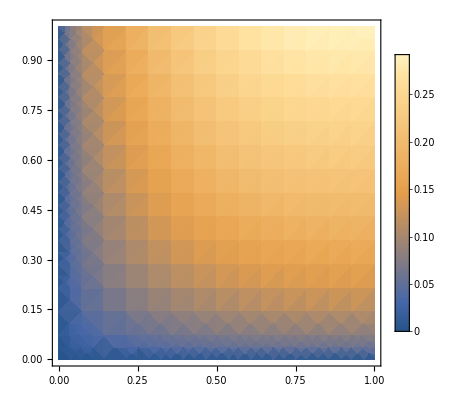

```mathematica
DensityPlot[10 √((h MM)/(453+302 h^3-3 h^6)) √(2/π),{h,0,1},{MM,0,1},PlotLegends->Automatic]
```

```mathematica
sol2/.{QQ->0.2,MM->1,h->0.5}//N
```

{{a2→-3.41314×10^-6 (11194.6+2896.37 a1-7. √((4263.81+250.271 a1)^2-5828.76 (-4908.04+361. a1+140.861 a1^2))),d2→-0.000163831 (-4263.81-250.271 a1+√((4263.81+250.271 a1)^2-5828.76 (-4908.04+361. a1+140.861 a1^2)))},{a2→-3.41314×10^-6 (11194.6+2896.37 a1+7. √((4263.81+250.271 a1)^2-5828.76 (-4908.04+361. a1+140.861 a1^2))),d2→0.000163831 (4263.81+250.271 a1+√((4263.81+250.271 a1)^2-5828.76 (-4908.04+361. a1+140.861 a1^2)))}}

```mathematica
p11=Plot[{ρ1/.sol2[[1]][[1]]}/.{QQ->0.2,MM->1},{h,0,1},PlotRange->All,PlotStyle->{Red,{Green,Dashed}}]
```

-Graphics-

```mathematica
p2=Plot[{ρ2/.sol2[[1]][[2]],ρ2/.sol2[[2]][[2]]}/.{QQ->0.2,MM->1},{h,0,1},PlotRange->All,PlotStyle->{Red,{Green,Dashed}}]
```

-Graphics-

```mathematica
(*Φexterior =Q/r;
Φinterior = Q/(2R)(3-r^2/R^2);
Einterior = -Grad[Φinterior,{r,θ,φ},"Spherical"][[1]];
Eexterior = -Grad[Φexterior,{r,θ,φ},"Spherical"][[1]];
Interior=1/2 Integrate[Einterior^2,{r,0,R}]+ Integrate[Q/r^3 Φinterior,{r,0,R}]
Integrate[1/r^3 Φinterior//Simplify,{r,0,R}]
Exterior = 1/2 Integrate[Eexterior^2,{r,R,Infinity}](*+Integrate[ (M Q)/r^3 Φexterior,{r,R,Infinity}]*)
(π^2 (ρ1+7 ρ2)^2)/(216 R^3)
Interior + Exterior//Simplify
(π^2 (ρ1+7 ρ2)^2+108 R^3 ∫_0^R (π^2 (r^2-3 R^2) (ρ1+7 ρ2)^2)/(72 r^3 R^3)ⅆr)/(108 R^3)
Limit[Interior + Exterior,R->0,Direction->"FromAbove"]
Solve[Interior + Exterior==M,ρ2]
Solve[(16 π^2)/(27 R^3)+∫_0^R -(8 π^2 (3-r^2/R^2))/(9 r^3 R)ⅆr==M,1]
Solve[(M Q (M Q-16 π R^3 ρ2))/(3 R^3)==M,ρ2]
Solve[(4 M π ((4 M π)/3-16 π R^3))/(9 R^3)==M,1]*)
```